#### Runge’s methods KZ

(x, y) - initial data
h - the grid step
f - initial function
b - the right boundary

#### 3 steps of order 3

```mathematica
solveDE[f_,x_,y_,h_,b_]:=Module[{x0,k1,k2,k3,y0,array={},arrayx={}},
x0=x;
y0=y;
While[x0<b,
k1=f[x0,y0];
k2=f[x0+h/2,y0+h k1/2];
k3=f[x0+h,y0-h k1+2h k2];
y0=y0+h(k1+4k2+k3)/6;
AppendTo[array,y0];
AppendTo[arrayx,x0];
x0+=h];{arrayx,array}//Transpose]
```

#### Let’s check our function with the integrated functions

```mathematica
f[x_,y_]:=Cos[3x]-4y
```

```mathematica
p=solveDE[f,0,1,0.01,1];
```

```mathematica
s=DSolve[{y'[x]==-4y[x]+Cos[3x],y[0]==1},y[x],x]⟦1,1⟧//Values
```

1/25 ⅇ^(-4 x) (21+4 ⅇ^(4 x) Cos[3 x]+3 ⅇ^(4 x) Sin[3 x])

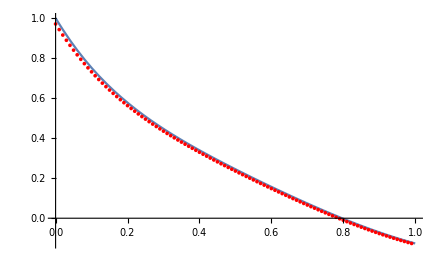

```mathematica
Plot[s/.x->k,{k,0,1},Epilog->{Red,PointSize[0.006],Point[p]}]
```

#### Classic Runge’s method of order 4

```mathematica
solveDE4order[x_,y_,h_,b_]:=Module[{x0,k1,k2,k3,k4,y0,array={},arrayx={}},
x0=x;
y0=y;
While[x0<b,
k1= f[x0,y0];
k2= f[x0+h/2,y0+h k1/2];
k3= f[x0+h/2,y0+h k2/2];
k4= f[x0+h,y0+h k3];
y0=y0+h(k1+2k2+2k3+k4)/6;
AppendTo[array,y0];
AppendTo[arrayx,x0];
x0+=h];{arrayx,array}//Transpose]
```

```mathematica
p2=solveDE4order[0,1,0.01,1];
```

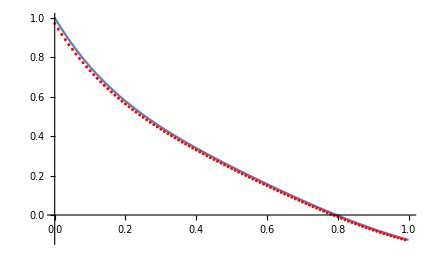

```mathematica
Show[{Plot[s/.x->k,{k,0,1}],Graphics[{Red,PointSize[0.005],Point[p2]}]},PlotRange->Full]
```

#### 2 steps of order 2

```mathematica
solveDE2order[x_,y_,h_,b_]:=Module[{x0,k1,k2,y0,array={},arrayx={}},
x0=x;
y0=y;
While[x0<b,
k1= f[x0,y0];
k2= f[x0+h/2,y0+h k1/2];
y0=y0+h k2;
AppendTo[array,y0];
AppendTo[arrayx,x0];
x0+=h];{arrayx,array}//Transpose]
```

```mathematica
p3=solveDE2order[0,1,0.01,1];
```

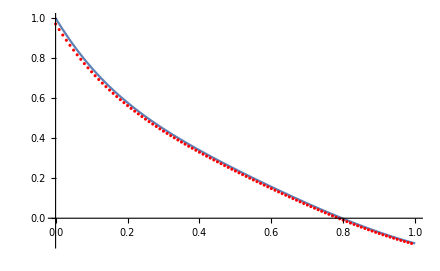

```mathematica
Show[{Plot[s/.x->k,{k,0,1}],Graphics[{Red,PointSize[0.005],Point[p3]}]},PlotRange->Full]
```